## Paths and Includes

```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
```

```mathematica
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

```mathematica
SetDirectory[basepath<>"/output"];
```

```mathematica
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
```

```mathematica
Needs["LatticeAnalysis`"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
<<"LatticeAnalysis`"
```

```mathematica
(* do not keep track of intermediate results *)
$HistoryLength=0;
```

## Configuration

We must provide information about the lattice spacing of the ensemble ourselves; it is not in the data base files (obviously)

```mathematica
lata=0.11403
```

0.11403

```mathematica
numsamples=All; (*number of samples to take for error estimates. Set to "All" if not in debug-mode!*)
```

The following line sets up blocking during the creation of Jackknife samples with block size 1.

```mathematica
MakeJacknifeSamplesB[x_]:=MakeJacknifeSamples[x,1];
```

```mathematica
thisquarkchannel="u-d";
```

## Constants

```mathematica
scalingNat = .1973270524; (* this is GeV*fm *)
```

```mathematica
quarkchannelshort[quarkchannel_]:=Switch[quarkchannel,"up","U","down","D","u-d","UminusD",_,Message["INVALID QUARK CHANNEL"]];
```

```mathematica
basedatapath1="/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_1/"
basedatapath2="/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_2/"
basedatapath3="/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_3/"
basedatapath4="/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_4/"
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_1/

/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_2/

/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_3/

/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_4/

```mathematica
exportdatapath1[quarkchannel_]:=basedatapath1<>quarkchannelshort[quarkchannel]<>"_"; 
exportdatapath2[quarkchannel_]:=basedatapath2<>quarkchannelshort[quarkchannel]<>"_"; 
exportdatapath3[quarkchannel_]:=basedatapath3<>quarkchannelshort[quarkchannel]<>"_"; 
exportdatapath4[quarkchannel_]:=basedatapath4<>quarkchannelshort[quarkchannel]<>"_";
```

```mathematica
resamplingext="_"<>"jn";
```

## Open Database

open the BIDATEX data base with the correlator data

```mathematica
platdb=BIDATEXReader[exportdatapath1[thisquarkchannel]<>"Plateaus"<>resamplingext<>".bidatex"]
(*platdbPm2=BIDATEXReader[exportdatapath2[thisquarkchannel]<>"Plateaus"<>resamplingext<>".bidatex"]
platdbPm3=BIDATEXReader[exportdatapath3[thisquarkchannel]<>"Plateaus"<>resamplingext<>".bidatex"]
platdbPm4=BIDATEXReader[exportdatapath4[thisquarkchannel]<>"Plateaus"<>resamplingext<>".bidatex"]*)
NEdb=BIDATEXReader[basedatapath1<>"NucleonEnergy"<>resamplingext<>".bidatex"]
(*NEdb2=BIDATEXReader[basedatapath2<>"NucleonEnergy"<>resamplingext<>".bidatex"]
NEdb3=BIDATEXReader[basedatapath3<>"NucleonEnergy"<>resamplingext<>".bidatex"]
NEdb4=BIDATEXReader[basedatapath4<>"NucleonEnergy"<>resamplingext<>".bidatex"]*)
```

< -MemDB- {aBDBIndex,correlatorType,gammaValue,linkPath,momTransfer,numberFilter,section,seqPropNum,sideExtent,sideLink,sideNum,sinkMom,sourceType,tSep,tSink,tSource,analysisStep,data}>

< -MemDB- {gammaValue,operation,section,sinkMom,sourceType,comment,tSource,sideLinks,linkPath,sideNum,sideExtent,correlatorType,seqPropNum,tSink,momTransfer,latsizeOrig,latsizeChopped,baryonObservableNr,aBDBIndex,data,numberFilter,energy,chisqrPDOF}>

```mathematica
(*Pm1latticeP0 = MemDBGet[NEdb1,MemDBSelect[NEdb1,{}],energy][[1]];
Pm2latticeP0 = MemDBGet[NEdb2,MemDBSelect[NEdb2,{}],energy][[1]];
Pm3latticeP0 = MemDBGet[NEdb3,MemDBSelect[NEdb3,{}],energy][[1]];
Pm4latticeP0 = MemDBGet[NEdb4,MemDBSelect[NEdb4,{}],energy][[1]];
Pm1latticeP1=(Pm1latticeP0/Pm1latticeP0)*((2*Pi)/(32));
Pm1latticePplus=(Pm1latticeP1+Pm1latticeP0)/Sqrt[2];
Pm1latticeMsquare =(Pm1latticeP0*Pm1latticeP0)-(Pm1latticeP1*Pm1latticeP1);
Pm1latticeM =Sqrt[Pm1latticeMsquare];
Print[" = E = (", Pm1latticeP0//OutputForm,")"]
Print[" =  = (", Pm1latticeP1//OutputForm,")"]
Print[" =  = (", Pm1latticePplus//OutputForm,")"]
Print["  = (", Pm1latticeM//OutputForm,")"]
Print["-----------"]
Pm2latticeP1=2*(Pm2latticeP0/Pm2latticeP0)*((2*Pi)/(32));
Pm2latticePplus=(Pm2latticeP1+Pm2latticeP0)/Sqrt[2];
Pm2latticeMsquare =(Pm2latticeP0*Pm2latticeP0)-(Pm2latticeP1*Pm2latticeP1);
Pm2latticeM =Sqrt[Pm2latticeMsquare];
Print[" = E = (", Pm2latticeP0//OutputForm,")"]
Print[" =  = (", Pm2latticeP1//OutputForm,")"]
Print[" =  = (", Pm2latticePplus//OutputForm,")"]
Print["  = (", Pm2latticeM//OutputForm,")"]*)
```

```mathematica
(*Union[MemDBGet[platdbPm1,MemDBSelect[platdbPm1,{numberFilter->Re}],sinkMom]][[1]][[1]]*)
```

```mathematica
(*v1[dbNo_,v3_]:=v3*v1BYv3[dbNo];
vinterpolation[dbNo_, gammaValueI_,numberFilterI_, linkPathI_, eta_]:=
(
platdbNo=ToExpression["platdbPm"<>ToString[dbNo]];
vlinks = Union[MemDBGet[platdbNo,MemDBSelect[platdbNo,{numberFilter->Re}],sideLink]];
vlinksv3 = Select[vlinks,Count[#,3]==eta&];
(*Print[vlinksv3];*)
vvectoranddata={};
Do[
v1data=PathToShift[vlinksv3[[i]],3];
correlatordata = MemDBGet[platdbNo,MemDBSelect[platdbNo,{gammaValue->gammaValueI,numberFilter->numberFilterI,linkPath->linkPathI,sideLink->vlinksv3[[i]]}],data];
AppendTo[vvectoranddata,{v1data,correlatordata[[1]]}]
,{i,Length[vlinksv3]}];
groupSamev=GroupBy[vvectoranddata,First->Last];
(*Print[vvectoranddata//OutputForm];
Print[groupSamev//OutputForm];*)
averagedTableEvengPlusImForv=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamev];
(*Print[averagedTableEvengPlusImForv//OutputForm];*)
dataforInterpolation ={};
v1dataforInterpolation ={};
Do[
AppendTo[v1dataforInterpolation,v1[dbNo,averagedTableEvengPlusImForv[[i]][[1]][[3]]]-averagedTableEvengPlusImForv[[i]][[1]][[1]]];
AppendTo[dataforInterpolation,averagedTableEvengPlusImForv[[i]][[2]]];
,{i, Length[averagedTableEvengPlusImForv]}];
(*Print[Transpose[{v1dataforInterpolation,dataforInterpolation}]//OutputForm];*)
fninterpol = Interpolation[Transpose[{v1dataforInterpolation,dataforInterpolation}],InterpolationOrder->2];
Return[fninterpol[0]];
);
Print[vinterpolation[dbNo = 1, gammaValueI = 4,numberFilterI = Re, linkPathI = {2,2,2,2,2,2,2}, eta = 8]//OutputForm]
Print[vinterpolation[dbNo = 2, gammaValueI = 4,numberFilterI = Re, linkPathI = {2,2,2,2,2,2,2}, eta = 8]//OutputForm]
Print[vinterpolation[dbNo = 3, gammaValueI = 4,numberFilterI = Re, linkPathI = {2,2,2,2,2,2,2}, eta = 8]//OutputForm]
Print[vinterpolation[dbNo = 4, gammaValueI = 4,numberFilterI = Re, linkPathI = {2,2,2,2,2,2,2}, eta = 8]//OutputForm]*)
```

```mathematica
(*xdata = {1,2,3,4,5,6,7,8,9,10};
ydata =Table[vinterpolation[gammaValueI = 1,numberFilterI = Re, linkPathI = {2,2,2,2,2,2,2}, eta = etav], {etav, xdata}]
fit = ResamplingFit2D[xdata,ydata,A*Exp[-B*v],v,{A, B}]
Print[fit[[1]]//OutputForm]
fitpara = fitSamples/.fit
fitA= fitpara[[All,2]][[All,1]]
fitB= fitpara[[All,2]][[All,2]]*)
```

```mathematica
vlink = Union[MemDBGet[platdb,MemDBSelect[platdb,{numberFilter->Re}],sideLink]];
vlinksv1 = Select[vlink,Count[#,3]==0&];
vlinksv1
MemDBGet[platdb,MemDBSelect[platdb,{sideLink->{}}],linkPath]//Union
```

{{},{1},{1,1},{1,1,1},{1,1,1,1},{1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

{{},{-2},{2},{-2,-2},{-2,-1},{-2,1},{-1,-2},{-1,2},{1,-2},{1,2},{2,-1},{2,1},{2,2},{-2,-2,-2},{-2,-1,-2},{-2,1,-2},{-1,-2,-1},{-1,2,-1},{1,-2,1},{1,2,1},{2,-1,2},{2,1,2},{2,2,2},{-2,-2,-2,-2},{-2,-1,-2,-1},{-2,1,-2,1},{-1,-2,-1,-2},{-1,2,-1,2},{1,-2,1,-2},{1,2,1,2},{2,-1,2,-1},{2,1,2,1},{2,2,2,2},{-2,-2,-2,-2,-2},{-1,-1,-2,-1,-1},{-1,-1,2,-1,-1},{1,1,-2,1,1},{1,1,2,1,1},{2,2,2,2,2},{-2,-2,-2,-2,-2,-2},{-2,-1,-2,-2,-1,-2},{-2,-1,-2,-1,-2,-1},{-2,1,-2,-2,1,-2},{-2,1,-2,1,-2,1},{-1,-2,-1,-2,-1,-2},{-1,-2,-1,-1,-2,-1},{-1,2,-1,-1,2,-1},{-1,2,-1,2,-1,2},{1,-2,1,-2,1,-2},{1,-2,1,1,-2,1},{1,2,1,1,2,1},{1,2,1,2,1,2},{2,-1,2,-1,2,-1},{2,-1,2,2,-1,2},{2,1,2,1,2,1},{2,1,2,2,1,2},{2,2,2,2,2,2},{-2,-2,-2,-2,-2,-2,-2},{2,2,2,2,2,2,2},{-2,-1,-2,-1,-2,-1,-2,-1},{-2,1,-2,1,-2,1,-2,1},{-1,-2,-1,-2,-1,-2,-1,-2},{-1,2,-1,2,-1,2,-1,2},{1,-2,1,-2,1,-2,1,-2},{1,2,1,2,1,2,1,2},{2,-1,2,-1,2,-1,2,-1},{2,1,2,1,2,1,2,1},{-2,-1,-2,-2,-1,-2,-2,-1,-2},{-2,1,-2,-2,1,-2,-2,1,-2},{-1,-2,-1,-1,-2,-1,-1,-2,-1},{-1,2,-1,-1,2,-1,-1,2,-1},{1,-2,1,1,-2,1,1,-2,1},{1,2,1,1,2,1,1,2,1},{2,-1,2,2,-1,2,2,-1,2},{2,1,2,2,1,2,2,1,2},{-2,-1,-2,-1,-2,-1,-2,-1,-2,-1},{-2,1,-2,1,-2,1,-2,1,-2,1},{-1,-2,-1,-2,-1,-2,-1,-2,-1,-2},{-1,-1,-2,-1,-1,-1,-1,-2,-1,-1},{-1,-1,2,-1,-1,-1,-1,2,-1,-1},{-1,2,-1,2,-1,2,-1,2,-1,2},{1,-2,1,-2,1,-2,1,-2,1,-2},{1,1,-2,1,1,1,1,-2,1,1},{1,1,2,1,1,1,1,2,1,1},{1,2,1,2,1,2,1,2,1,2},{2,-1,2,-1,2,-1,2,-1,2,-1},{2,1,2,1,2,1,2,1,2,1}}

```mathematica
AllLinkPathList = MemDBGet[platdb,MemDBSelect[platdb,{gammaValue->8,numberFilter->Re}],linkPath];
Print[ "Total No. linkPath = ",Length[AllLinkPathList]]
Print[ "Total No. Distinct linkPath = ",CountDistinct[AllLinkPathList]]
DistinctLinkPaths= DeleteDuplicates[AllLinkPathList];
(*Do[Print[i,") ",PathToShift[DistinctLinkPaths[[i+1]],3],"<------->",DistinctLinkPaths[[i+1]], "<------->", MemDBGet[platdb1,MemDBSelect[platdb1,{linkPath->DistinctLinkPaths[[i+1]]}],sideNum]//DeleteDuplicates],{i,CountDistinct[AllLinkPathList]-1}]*)
Print["linkPaths -> {} are skipped"];
bveclinkPathsideNumLIST={};
Do[
AppendTo[bveclinkPathsideNumLIST,{PathToShift[DistinctLinkPaths[[i+1]],3],DistinctLinkPaths[[i+1]]}],{i,CountDistinct[AllLinkPathList]-1}]
(*bveclinkPathsideNumLIST//MatrixForm*)
bveclinkPathsideNumLISTforbL0=Select[bveclinkPathsideNumLIST,#[[1,1]]==0&];
bveclinkPathsideNumLISTforbLpositive=Select[bveclinkPathsideNumLIST,#[[1,1]]>0&];
bveclinkPathsideNumLISTforbLnegative=Select[bveclinkPathsideNumLIST,#[[1,1]]<0&];
b2list= Union[bveclinkPathsideNumLIST[[All,1]][[All,2]]];
b1list= Union[bveclinkPathsideNumLIST[[All,1]][[All,1]]];
Print["b2 = ",b2list]
Print["b1 = ",b1list]
bveclinkPathsideNumLISTforbL0//MatrixForm
bveclinkPathsideNumLISTforbLpositive//MatrixForm
bveclinkPathsideNumLISTforbLnegative//MatrixForm
bveclinkPathsideNumLISTforbL0//Length
bveclinkPathsideNumLISTforbLpositive//Length
bveclinkPathsideNumLISTforbLnegative//Length
noError=True;
Do[If[(bveclinkPathsideNumLISTforbLpositive[[i,1]][[1]]+bveclinkPathsideNumLISTforbLnegative[[i,1]][[1]])=!=0,Print["Mismatch in finding   at bveclinkPathsideNumLISTforbLpositive[",i, "]"];noError=False;],{i,Length[bveclinkPathsideNumLISTforbLpositive]}];
If[noError,Print["✓ Checked: linkPaths corresponding to   are found "]];
```

Total No. linkPath = 7225

Total No. Distinct linkPath = 87

linkPaths -> {} are skipped

b2 = {-7,-6,-5,-4,-3,-2,-1,1,2,3,4,5,6,7}

b1 = {-8,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,8}

({0,1,0} | {2}
{0,2,0} | {2,2}
{0,3,0} | {2,2,2}
{0,4,0} | {2,2,2,2}
{0,5,0} | {2,2,2,2,2}
{0,6,0} | {2,2,2,2,2,2}
{0,7,0} | {2,2,2,2,2,2,2}
{0,-1,0} | {-2}
{0,-2,0} | {-2,-2}
{0,-3,0} | {-2,-2,-2}
{0,-4,0} | {-2,-2,-2,-2}
{0,-5,0} | {-2,-2,-2,-2,-2}
{0,-6,0} | {-2,-2,-2,-2,-2,-2}
{0,-7,0} | {-2,-2,-2,-2,-2,-2,-2})

({1,1,0} | {2,1}
{2,2,0} | {2,1,2,1}
{3,3,0} | {2,1,2,1,2,1}
{4,4,0} | {2,1,2,1,2,1,2,1}
{5,5,0} | {2,1,2,1,2,1,2,1,2,1}
{1,1,0} | {1,2}
{2,2,0} | {1,2,1,2}
{3,3,0} | {1,2,1,2,1,2}
{4,4,0} | {1,2,1,2,1,2,1,2}
{5,5,0} | {1,2,1,2,1,2,1,2,1,2}
{1,2,0} | {2,1,2}
{2,4,0} | {2,1,2,2,1,2}
{3,6,0} | {2,1,2,2,1,2,2,1,2}
{2,1,0} | {1,2,1}
{4,2,0} | {1,2,1,1,2,1}
{6,3,0} | {1,2,1,1,2,1,1,2,1}
{4,1,0} | {1,1,2,1,1}
{8,2,0} | {1,1,2,1,1,1,1,2,1,1}
{1,-1,0} | {-2,1}
{2,-2,0} | {-2,1,-2,1}
{3,-3,0} | {-2,1,-2,1,-2,1}
{4,-4,0} | {-2,1,-2,1,-2,1,-2,1}
{5,-5,0} | {-2,1,-2,1,-2,1,-2,1,-2,1}
{1,-1,0} | {1,-2}
{2,-2,0} | {1,-2,1,-2}
{3,-3,0} | {1,-2,1,-2,1,-2}
{4,-4,0} | {1,-2,1,-2,1,-2,1,-2}
{5,-5,0} | {1,-2,1,-2,1,-2,1,-2,1,-2}
{1,-2,0} | {-2,1,-2}
{2,-4,0} | {-2,1,-2,-2,1,-2}
{3,-6,0} | {-2,1,-2,-2,1,-2,-2,1,-2}
{2,-1,0} | {1,-2,1}
{4,-2,0} | {1,-2,1,1,-2,1}
{6,-3,0} | {1,-2,1,1,-2,1,1,-2,1}
{4,-1,0} | {1,1,-2,1,1}
{8,-2,0} | {1,1,-2,1,1,1,1,-2,1,1})

({-1,1,0} | {2,-1}
{-2,2,0} | {2,-1,2,-1}
{-3,3,0} | {2,-1,2,-1,2,-1}
{-4,4,0} | {2,-1,2,-1,2,-1,2,-1}
{-5,5,0} | {2,-1,2,-1,2,-1,2,-1,2,-1}
{-1,1,0} | {-1,2}
{-2,2,0} | {-1,2,-1,2}
{-3,3,0} | {-1,2,-1,2,-1,2}
{-4,4,0} | {-1,2,-1,2,-1,2,-1,2}
{-5,5,0} | {-1,2,-1,2,-1,2,-1,2,-1,2}
{-1,2,0} | {2,-1,2}
{-2,4,0} | {2,-1,2,2,-1,2}
{-3,6,0} | {2,-1,2,2,-1,2,2,-1,2}
{-2,1,0} | {-1,2,-1}
{-4,2,0} | {-1,2,-1,-1,2,-1}
{-6,3,0} | {-1,2,-1,-1,2,-1,-1,2,-1}
{-4,1,0} | {-1,-1,2,-1,-1}
{-8,2,0} | {-1,-1,2,-1,-1,-1,-1,2,-1,-1}
{-1,-1,0} | {-2,-1}
{-2,-2,0} | {-2,-1,-2,-1}
{-3,-3,0} | {-2,-1,-2,-1,-2,-1}
{-4,-4,0} | {-2,-1,-2,-1,-2,-1,-2,-1}
{-5,-5,0} | {-2,-1,-2,-1,-2,-1,-2,-1,-2,-1}
{-1,-1,0} | {-1,-2}
{-2,-2,0} | {-1,-2,-1,-2}
{-3,-3,0} | {-1,-2,-1,-2,-1,-2}
{-4,-4,0} | {-1,-2,-1,-2,-1,-2,-1,-2}
{-5,-5,0} | {-1,-2,-1,-2,-1,-2,-1,-2,-1,-2}
{-1,-2,0} | {-2,-1,-2}
{-2,-4,0} | {-2,-1,-2,-2,-1,-2}
{-3,-6,0} | {-2,-1,-2,-2,-1,-2,-2,-1,-2}
{-2,-1,0} | {-1,-2,-1}
{-4,-2,0} | {-1,-2,-1,-1,-2,-1}
{-6,-3,0} | {-1,-2,-1,-1,-2,-1,-1,-2,-1}
{-4,-1,0} | {-1,-1,-2,-1,-1}
{-8,-2,0} | {-1,-1,-2,-1,-1,-1,-1,-2,-1,-1})

14

36

36

✓ Checked: linkPaths corresponding to   are found

```mathematica
(*Print["From NucleonEnergy dataset"]
NEdb1=BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_1/NucleonEnergy_jn.bidatex"]
latticeP0=MemDBGet[NEdb1,MemDBSelect[NEdb1,{}],energy][[1]];
latticeP1=(latticeP0/latticeP0)*((2*Pi)/(32));
latticePplus=(latticeP1+latticeP0)/Sqrt[2];
latticeMsquare =(latticeP0*latticeP0)-(latticeP1*latticeP1);
latticeM =Sqrt[latticeMsquare];
Print[" = E = (", latticeP0//OutputForm,")"]
Print[" =  = (", latticeP1//OutputForm,")"]
Print[" =  = (", latticePplus//OutputForm,")"]
Print["  = (", latticeM//OutputForm,")"]*)
```

```mathematica
dbNo = 1; (*change this number according to the momentum selection*)
P0= MemDBGet[NEdb,MemDBSelect[NEdb,{}],energy][[1]];
II=(P0/P0);
P1 = dbNo*II*((2*Pi)/(32));
Msquare =(P0*P0)-(P1*P1);
M =Sqrt[Msquare];
Pplus=(P1+P0)/Sqrt[2];
S3=1;
Print[Pplus]
ztahat=Sqrt[(P1*P1)/(M*M*(((M*M)/(P1*P1))+(2*II)))];
v1byv3jakk=(M*ztahat)/(P1*(Sqrt[II-((M*M*ztahat*ztahat)/(P1*P1))]));
v1BYv3=Abs[MakeErrBars[{{1,v1byv3jakk}}][[1]][[1]][[2]]];
v1[v3_]:=v3*v1BYv3;

vinterpolation[gammaValueI_,numberFilterI_, linkPathI_, eta_]:=
(
vlinks = Union[MemDBGet[platdb,MemDBSelect[platdb,{numberFilter->Re}],sideLink]];
vlinksv3 = Select[vlinks,Count[#,3]==eta&];
(*Print[vlinksv3];*)
vvectoranddata={};
Do[
v1data=PathToShift[vlinksv3[[i]],3];
correlatordata = MemDBGet[platdb,MemDBSelect[platdb,{gammaValue->gammaValueI,numberFilter->numberFilterI,linkPath->linkPathI,sideLink->vlinksv3[[i]]}],data];
AppendTo[vvectoranddata,{v1data,correlatordata[[1]]}]
,{i,Length[vlinksv3]}];
groupSamev=GroupBy[vvectoranddata,First->Last];
(*Print[vvectoranddata//OutputForm];
Print[groupSamev//OutputForm];*)
averagedTableEvengPlusImForv=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamev];
(*Print[averagedTableEvengPlusImForv//OutputForm];*)
dataforInterpolation ={};
v1dataforInterpolation ={};
Do[
AppendTo[v1dataforInterpolation,v1[averagedTableEvengPlusImForv[[i]][[1]][[3]]]-averagedTableEvengPlusImForv[[i]][[1]][[1]]];
AppendTo[dataforInterpolation,averagedTableEvengPlusImForv[[i]][[2]]];
,{i, Length[averagedTableEvengPlusImForv]}];
(*Print[Transpose[{v1dataforInterpolation,dataforInterpolation}]//OutputForm];*)
fninterpol = Interpolation[Transpose[{v1dataforInterpolation,dataforInterpolation}],InterpolationOrder->2];
Return[fninterpol[0]];
);

GivebPbbsquareA12B[etavalue_]:=(
bvectorA12B = {};

Do[
bl0g8Im = vinterpolation[gammaValueI = 8,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbL0[[i,2]], eta = etavalue];
bl0g1Re = vinterpolation[gammaValueI = 1,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbL0[[i,2]], eta = etavalue];
bl0g3Re = vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbL0[[i,2]], eta = etavalue];
b2valuebL0= bveclinkPathsideNumLISTforbL0[[i,1]][[2]];

(*bl0A12B = ((1/(2*M*S3*b2valuebL0*Pplus))*((-bl0g1Re/Sqrt[2])-(bl0g8Im/Sqrt[2])-(((P1-P0)*bl0g3Re)/(v1BYv3*P0))));*)
bl0A12=(-b2valuebL0/(2*M*P0*(b2valuebL0*b2valuebL0)*S3))*(bl0g1Re-((b2valuebL0*b2valuebL0)*bl0g3Re/(b2valuebL0*b2valuebL0*v1BYv3)));
bl0B8=(1/(2*Sqrt[2]*Pplus*b2valuebL0*M*S3))*(bl0g8Im+(P1*bl0g3Re/P0*v1BYv3)-((b2valuebL0*b2valuebL0*P1/(P0*(b2valuebL0*b2valuebL0)))*(bl0g1Re-((b2valuebL0*b2valuebL0)*bl0g3Re/(b2valuebL0*b2valuebL0*v1BYv3))) ));
bl0A12B= bl0A12-bl0B8;
AppendTo[bvectorA12B,{bveclinkPathsideNumLISTforbL0[[i,1]],bl0A12B}];
  ,{i,Length[bveclinkPathsideNumLISTforbL0]}];

vlink = Union[MemDBGet[platdb,MemDBSelect[platdb,{numberFilter->Re}],sideLink]];
vlinksv1 = Select[vlink,Count[#,3]==0&];

(*Do[
v30bl0g8Im = MemDBGet[platdb,MemDBSelect[platdb,{gammaValue-> 8,numberFilter->Im, linkPath->bveclinkPathsideNumLISTforbL0[[i,2]], sideLink -> vlinksv1[[etavalue+1]]}],data][[1]];
v30bl0g1Re =MemDBGet[platdb,MemDBSelect[platdb,{gammaValue-> 1,numberFilter->Re, linkPath->bveclinkPathsideNumLISTforbL0[[i,2]], sideLink -> vlinksv1[[etavalue+1]]}],data][[1]];
v30bl0g3Re = MemDBGet[platdb,MemDBSelect[platdb,{gammaValue-> 4,numberFilter->Re, linkPath->bveclinkPathsideNumLISTforbL0[[i,2]], sideLink -> vlinksv1[[etavalue+1]]}],data][[1]];
v30b2valuebL0= bveclinkPathsideNumLISTforbL0[[i,1]][[2]];

v30bl0A12=(-v30b2valuebL0/(2*M*P0*(v30b2valuebL0*v30b2valuebL0)*S3))*(v30bl0g1Re);
v30bl0B8=(1/(2*Sqrt[2]*Pplus*v30b2valuebL0*M*S3))*(v30bl0g8Im-((v30b2valuebL0*v30b2valuebL0*P1/(P0*(v30b2valuebL0*v30b2valuebL0)))*(v30bl0g1Re )));
v30bl0A12B= v30bl0A12-v30bl0B8;
AppendTo[bvectorA12B,{bveclinkPathsideNumLISTforbL0[[i,1]],v30bl0A12B}];
  ,{i,Length[bveclinkPathsideNumLISTforbL0]}];*)

Do[
blPg8Im = vinterpolation[gammaValueI = 8,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbLpositive[[i,2]], eta = etavalue];
blPg1Re = vinterpolation[gammaValueI = 1,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLpositive[[i,2]], eta = etavalue];
blPg2Re = vinterpolation[gammaValueI = 2,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLpositive[[i,2]], eta = etavalue];
blPg3Re = vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLpositive[[i,2]], eta = etavalue];
b2valuebLP= bveclinkPathsideNumLISTforbLpositive[[i,1]][[2]];
b1valuebLP= bveclinkPathsideNumLISTforbLpositive[[i,1]][[1]];

blNg8Im=vinterpolation[gammaValueI = 8,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbLnegative[[i,2]], eta = etavalue];
blNg1Re=vinterpolation[gammaValueI = 1,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLnegative[[i,2]], eta = etavalue];
blNg2Re=vinterpolation[gammaValueI = 2,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLnegative[[i,2]], eta = etavalue];
blNg3Re=vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLnegative[[i,2]], eta = etavalue];
b2valuebLN= bveclinkPathsideNumLISTforbLnegative[[i,1]][[2]];
b1valuebLN= bveclinkPathsideNumLISTforbLnegative[[i,1]][[1]];

blPA12=(-b2valuebLP/(2*M*P0*(b2valuebLP*b2valuebLP+b1valuebLP*b1valuebLP)*S3))*(blPg1Re+(blPg2Re*b1valuebLP/b2valuebLP)-((b2valuebLP*b2valuebLP-b1valuebLP*b1valuebLP)*blPg3Re/(b2valuebLP*b2valuebLP*v1BYv3)));

blNA12=(-b2valuebLN/(2*M*P0*(b2valuebLN*b2valuebLN+b1valuebLN*b1valuebLN)*S3))*(blNg1Re+(blNg2Re*b1valuebLN/b2valuebLN)-((b2valuebLN*b2valuebLN-b1valuebLN*b1valuebLN)*blNg3Re/(b2valuebLN*b2valuebLN*v1BYv3)));

blPB8=(1/(2*Sqrt[2]*Pplus*b2valuebLP*M*S3))*(blPg8Im+(P1*blPg3Re/P0*v1BYv3)-((b2valuebLP*b2valuebLP*P1/(P0*(b1valuebLP*b1valuebLP+b2valuebLP*b2valuebLP)))*(blPg1Re+(blPg2Re*b1valuebLP/b2valuebLP)-((b2valuebLP*b2valuebLP-b1valuebLP*b1valuebLP)*blPg3Re/(b2valuebLP*b2valuebLP*v1BYv3))) ));

blNB8=(1/(2*Sqrt[2]*Pplus*b2valuebLN*M*S3))*(blNg8Im+(P1*blNg3Re/P0*v1BYv3)-((b2valuebLN*b2valuebLN*P1/(P0*(b1valuebLN*b1valuebLN+b2valuebLN*b2valuebLN)))*(blNg1Re+(blNg2Re*b1valuebLN/b2valuebLN)-((b2valuebLN*b2valuebLN-b1valuebLN*b1valuebLN)*blNg3Re/(b2valuebLN*b2valuebLN*v1BYv3))) ));
blPA12B=blPA12-blPB8;
blNA12B=blNA12-blNB8;
blEvenA12B= (blPA12B+blNA12B)/2;

AppendTo[bvectorA12B,{bveclinkPathsideNumLISTforbLpositive[[i,1]],blEvenA12B}];
AppendTo[bvectorA12B,{bveclinkPathsideNumLISTforbLnegative[[i,1]],blEvenA12B}];
,{i,Length[bveclinkPathsideNumLISTforbLpositive]}];

(*Do[
v30blPg8Im = MemDBGet[platdb,MemDBSelect[platdb,{gammaValue-> 8,numberFilter->Im, linkPath->bveclinkPathsideNumLISTforbLpositive[[i,2]], sideLink -> vlinksv1[[etavalue+1]]}],data][[1]];
v30blPg1Re =MemDBGet[platdb,MemDBSelect[platdb,{gammaValue-> 1,numberFilter->Re, linkPath->bveclinkPathsideNumLISTforbLpositive[[i,2]], sideLink -> vlinksv1[[etavalue+1]]}],data][[1]];
v30blPg2Re =MemDBGet[platdb,MemDBSelect[platdb,{gammaValue-> 2,numberFilter->Re, linkPath->bveclinkPathsideNumLISTforbLpositive[[i,2]], sideLink -> vlinksv1[[etavalue+1]]}],data][[1]];
v30blPg3Re = MemDBGet[platdb,MemDBSelect[platdb,{gammaValue-> 4,numberFilter->Re, linkPath->bveclinkPathsideNumLISTforbLpositive[[i,2]], sideLink -> vlinksv1[[etavalue+1]]}],data][[1]];
v30b2valuebLP= bveclinkPathsideNumLISTforbLpositive[[i,1]][[2]];
v30b1valuebLP= bveclinkPathsideNumLISTforbLpositive[[i,1]][[1]];

v30blNg8Im = MemDBGet[platdb,MemDBSelect[platdb,{gammaValue-> 8,numberFilter->Im, linkPath->bveclinkPathsideNumLISTforbLnegative[[i,2]], sideLink -> vlinksv1[[etavalue+1]]}],data][[1]];
v30blNg1Re =MemDBGet[platdb,MemDBSelect[platdb,{gammaValue-> 1,numberFilter->Re, linkPath->bveclinkPathsideNumLISTforbLnegative[[i,2]], sideLink -> vlinksv1[[etavalue+1]]}],data][[1]];
v30blNg2Re =MemDBGet[platdb,MemDBSelect[platdb,{gammaValue-> 2,numberFilter->Re, linkPath->bveclinkPathsideNumLISTforbLnegative[[i,2]], sideLink -> vlinksv1[[etavalue+1]]}],data][[1]];
v30blNg3Re = MemDBGet[platdb,MemDBSelect[platdb,{gammaValue-> 4,numberFilter->Re, linkPath->bveclinkPathsideNumLISTforbLnegative[[i,2]], sideLink -> vlinksv1[[etavalue+1]]}],data][[1]];
v30b2valuebLN= bveclinkPathsideNumLISTforbLnegative[[i,1]][[2]];
v30b1valuebLN= bveclinkPathsideNumLISTforbLnegative[[i,1]][[1]];

v30blPA12=(-v30b2valuebLP/(2*M*P0*(v30b2valuebLP*v30b2valuebLP+v30b1valuebLP*v30b1valuebLP)*S3))*(v30blPg1Re+(v30blPg2Re*v30b1valuebLP/v30b2valuebLP));

v30blNA12=(-v30b2valuebLN/(2*M*P0*(v30b2valuebLN*v30b2valuebLN+v30b1valuebLN*v30b1valuebLN)*S3))*(v30blNg1Re+(v30blNg2Re*v30b1valuebLN/v30b2valuebLN));

v30blPB8=(1/(2*Sqrt[2]*Pplus*v30b2valuebLP*M*S3))*(v30blPg8Im-((v30b2valuebLP*v30b2valuebLP*P1/(P0*(v30b1valuebLP*v30b1valuebLP+v30b2valuebLP*v30b2valuebLP)))*(v30blPg1Re+(v30blPg2Re*v30b1valuebLP/v30b2valuebLP) )));

v30blNB8=(1/(2*Sqrt[2]*Pplus*v30b2valuebLN*M*S3))*(v30blNg8Im-((v30b2valuebLN*v30b2valuebLN*P1/(P0*(v30b1valuebLN*v30b1valuebLN+v30b2valuebLN*v30b2valuebLN)))*(v30blNg1Re+(v30blNg2Re*v30b1valuebLN/v30b2valuebLN) )));
v30blPA12B=v30blPA12-v30blPB8;
v30blNA12B=v30blNA12-v30blNB8;
v30blEvenA12B= (v30blPA12B+v30blNA12B)/2;
  
AppendTo[bvectorA12B,{bveclinkPathsideNumLISTforbLpositive[[i,1]],v30blEvenA12B}];
AppendTo[bvectorA12B,{bveclinkPathsideNumLISTforbLnegative[[i,1]],v30blEvenA12B}];
,{i,Length[bveclinkPathsideNumLISTforbLpositive]}];*)

groupSameb=GroupBy[bvectorA12B,First->Last];
averagedSamebvectorA12B=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSameb];
bPbsquareA12B={};
Do[
AppendTo[bPbsquareA12B,{{-averagedSamebvectorA12B[[j]][[1]][[1]]*dbNo*((2*Pi)/(32)),((averagedSamebvectorA12B[[j]][[1]][[1]]*averagedSamebvectorA12B[[j]][[1]][[1]])+(averagedSamebvectorA12B[[j]][[1]][[2]]*averagedSamebvectorA12B[[j]][[1]][[2]]))},averagedSamebvectorA12B[[j]][[2]]}]
,{j,Length[averagedSamebvectorA12B]}];
Return[bvectorA12B];
)

PlotA12B[etavalue_]:=(
TablePbbsquareA12B = GivebPbbsquareA12B[etavalue];
groupSamebsquare=GroupBy[TablePbbsquareA12B,First->Last];
PbaveragedbsquareA12B=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamebsquare];
Print["\n etavalue = ", etavalue];
(*Print["✓ Same  with different linkPath are averaged\n"];*)
bsquarelist= Union[PbaveragedbsquareA12B[[All,1]][[All,2]]];
PbLlist= Union[PbaveragedbsquareA12B[[All,1]][[All,1]]];
PbA2BforDiffbsquare={};
Do[
PbA2B=Transpose[{Select[PbaveragedbsquareA12B, #[[1,2]]==bsquarelist[[i]]&][[All,1]][[All,1]],Select[PbaveragedbsquareA12B, #[[1,2]]==bsquarelist[[i]]&][[All,2]]}];
AppendTo[PbA2BforDiffbsquare,PbA2B];
 ,{i,Length[bsquarelist]}];
PltA12B= ErrorListPlot[Table[MakeErrBars[PbA2BforDiffbsquare[[b2]]],{b2, Length[bsquarelist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotRange->All
, PlotLegends->Table[" = "<>ToString[bsquarelist[[b2]]],{b2,Length[bsquarelist]}]];
Return[Print[PltA12B]];
)
```

⟨0.6006(19)⟩_(RowBox[{)

```mathematica
PbbsqA12Bvalueserrbars[etavalue_]:=(
PbbsqA12BvalueerrbarLIST={};
TablePbbsquareA12B = GivebPbbsquareA12B[etavalue];
groupSamebsquare=GroupBy[TablePbbsquareA12B,First->Last];
PbaveragedbsquareA12B=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamebsquare];
PbbsqA12Bvalueerrbar = MakeErrBars[PbaveragedbsquareA12B];
Do[
AppendTo[PbbsqA12BvalueerrbarLIST, {etavalue, PbbsqA12Bvalueerrbar[[i]][[1]][[1]][[1]] ,PbbsqA12Bvalueerrbar[[i]][[1]][[1]][[2]],  PbbsqA12Bvalueerrbar[[i]][[1]][[2]],  PbbsqA12Bvalueerrbar[[i]][[2]][[1]][[2]]}];
,{i, Length[PbbsqA12Bvalueerrbar]}];
Return[PbbsqA12BvalueerrbarLIST]
)
```

```mathematica
GivebPbbsquareA12B[8]
```

{{{0,1,0},⟨-0.019(11)⟩_(RowBox[{)},{{0,2,0},⟨-0.0046(21)⟩_(RowBox[{)},{{0,3,0},⟨-0.0015(11)⟩_(RowBox[{)},{{0,4,0},⟨-0.00138(72)⟩_(RowBox[{)},{{0,5,0},⟨-990(520) × 10⟩_(RowBox[{)},{{0,6,0},⟨-860(420) × 10⟩_(RowBox[{)},{{0,7,0},⟨-640(340) × 10⟩_(RowBox[{)},{{0,-1,0},⟨-0.023(11)⟩_(RowBox[{)},{{0,-2,0},⟨-0.0063(21)⟩_(RowBox[{)},{{0,-3,0},⟨-0.0017(11)⟩_(RowBox[{)},{{0,-4,0},⟨-0.00105(70)⟩_(RowBox[{)},{{0,-5,0},⟨-220(480) × 10⟩_(RowBox[{)},{{0,-6,0},⟨-140(380) × 10⟩_(RowBox[{)},{{0,-7,0},⟨-0.00007 ± 0.0003⟩_(RowBox[{)},{{0,1,0},⟨-0.1301(51)⟩_(RowBox[{)},{{0,2,0},⟨-0.03048(99)⟩_(RowBox[{)},{{0,3,0},⟨-0.00996(46)⟩_(RowBox[{)},{{0,4,0},⟨-0.00435(31)⟩_(RowBox[{)},{{0,5,0},⟨-0.00234(23)⟩_(RowBox[{)},{{0,6,0},⟨-0.00116(17)⟩_(RowBox[{)},{{0,7,0},⟨-670(150) × 10⟩_(RowBox[{)},{{0,-1,0},⟨-0.1276(53)⟩_(RowBox[{)},{{0,-2,0},⟨-0.0291(10)⟩_(RowBox[{)},{{0,-3,0},⟨-0.00874(48)⟩_(RowBox[{)},{{0,-4,0},⟨-0.00372(31)⟩_(RowBox[{)},{{0,-5,0},⟨-0.00200(22)⟩_(RowBox[{)},{{0,-6,0},⟨-920(170) × 10⟩_(RowBox[{)},{{0,-7,0},⟨-300(140) × 10⟩_(RowBox[{)},{{1,1,0},⟨-0.0146(27)⟩_(RowBox[{)},{{-1,1,0},⟨-0.0146(27)⟩_(RowBox[{)},{{2,2,0},⟨-0.00253(45)⟩_(RowBox[{)},{{-2,2,0},⟨-0.00253(45)⟩_(RowBox[{)},{{3,3,0},⟨-790(240) × 10⟩_(RowBox[{)},{{-3,3,0},⟨-790(240) × 10⟩_(RowBox[{)},{{4,4,0},⟨-530(170) × 10⟩_(RowBox[{)},{{-4,4,0},⟨-530(170) × 10⟩_(RowBox[{)},{{5,5,0},⟨-220(110) × 10⟩_(RowBox[{)},{{-5,5,0},⟨-220(110) × 10⟩_(RowBox[{)},{{1,1,0},⟨-0.0145(27)⟩_(RowBox[{)},{{-1,1,0},⟨-0.0145(27)⟩_(RowBox[{)},{{2,2,0},⟨-0.00258(44)⟩_(RowBox[{)},{{-2,2,0},⟨-0.00258(44)⟩_(RowBox[{)},{{3,3,0},⟨-740(240) × 10⟩_(RowBox[{)},{{-3,3,0},⟨-740(240) × 10⟩_(RowBox[{)},{{4,4,0},⟨-440(170) × 10⟩_(RowBox[{)},{{-4,4,0},⟨-440(170) × 10⟩_(RowBox[{)},{{5,5,0},⟨-230(110) × 10⟩_(RowBox[{)},{{-5,5,0},⟨-230(110) × 10⟩_(RowBox[{)},{{1,2,0},⟨-0.0036(11)⟩_(RowBox[{)},{{-1,2,0},⟨-0.0036(11)⟩_(RowBox[{)},{{2,4,0},⟨-520(350) × 10⟩_(RowBox[{)},{{-2,4,0},⟨-520(350) × 10⟩_(RowBox[{)},{{3,6,0},⟨-420(180) × 10⟩_(RowBox[{)},{{-3,6,0},⟨-420(180) × 10⟩_(RowBox[{)},{{2,1,0},⟨-0.0082(21)⟩_(RowBox[{)},{{-2,1,0},⟨-0.0082(21)⟩_(RowBox[{)},{{4,2,0},⟨-340(650) × 10⟩_(RowBox[{)},{{-4,2,0},⟨-340(650) × 10⟩_(RowBox[{)},{{6,3,0},⟨390(370) × 10⟩_(RowBox[{)},{{-6,3,0},⟨390(370) × 10⟩_(RowBox[{)},{{4,1,0},⟨-0.0009 ± 0.0018⟩_(RowBox[{)},{{-4,1,0},⟨-0.0009 ± 0.0018⟩_(RowBox[{)},{{8,2,0},⟨-0.00007 ± 0.00066⟩_(RowBox[{)},{{-8,2,0},⟨-0.00007 ± 0.00066⟩_(RowBox[{)},{{1,-1,0},⟨-0.0132(27)⟩_(RowBox[{)},{{-1,-1,0},⟨-0.0132(27)⟩_(RowBox[{)},{{2,-2,0},⟨-0.00310(48)⟩_(RowBox[{)},{{-2,-2,0},⟨-0.00310(48)⟩_(RowBox[{)},{{3,-3,0},⟨-350(250) × 10⟩_(RowBox[{)},{{-3,-3,0},⟨-350(250) × 10⟩_(RowBox[{)},{{4,-4,0},⟨0.00003 ± 0.00015⟩_(RowBox[{)},{{-4,-4,0},⟨0.00003 ± 0.00015⟩_(RowBox[{)},{{5,-5,0},⟨0.00008 ± 0.00011⟩_(RowBox[{)},{{-5,-5,0},⟨0.00008 ± 0.00011⟩_(RowBox[{)},{{1,-1,0},⟨-0.0129(27)⟩_(RowBox[{)},{{-1,-1,0},⟨-0.0129(27)⟩_(RowBox[{)},{{2,-2,0},⟨-0.00299(48)⟩_(RowBox[{)},{{-2,-2,0},⟨-0.00299(48)⟩_(RowBox[{)},{{3,-3,0},⟨-280(260) × 10⟩_(RowBox[{)},{{-3,-3,0},⟨-280(260) × 10⟩_(RowBox[{)},{{4,-4,0},⟨0.00004 ± 0.00016⟩_(RowBox[{)},{{-4,-4,0},⟨0.00004 ± 0.00016⟩_(RowBox[{)},{{5,-5,0},⟨130(120) × 10⟩_(RowBox[{)},{{-5,-5,0},⟨130(120) × 10⟩_(RowBox[{)},{{1,-2,0},⟨-0.0052(12)⟩_(RowBox[{)},{{-1,-2,0},⟨-0.0052(12)⟩_(RowBox[{)},{{2,-4,0},⟨-220(350) × 10⟩_(RowBox[{)},{{-2,-4,0},⟨-220(350) × 10⟩_(RowBox[{)},{{3,-6,0},⟨-160(180) × 10⟩_(RowBox[{)},{{-3,-6,0},⟨-160(180) × 10⟩_(RowBox[{)},{{2,-1,0},⟨-0.0057(22)⟩_(RowBox[{)},{{-2,-1,0},⟨-0.0057(22)⟩_(RowBox[{)},{{4,-2,0},⟨-0.00153(67)⟩_(RowBox[{)},{{-4,-2,0},⟨-0.00153(67)⟩_(RowBox[{)},{{6,-3,0},⟨300(360) × 10⟩_(RowBox[{)},{{-6,-3,0},⟨300(360) × 10⟩_(RowBox[{)},{{4,-1,0},⟨-0.0023(19)⟩_(RowBox[{)},{{-4,-1,0},⟨-0.0023(19)⟩_(RowBox[{)},{{8,-2,0},⟨-490(660) × 10⟩_(RowBox[{)},{{-8,-2,0},⟨-490(660) × 10⟩_(RowBox[{)},{{1,1,0},⟨-0.1269(44)⟩_(RowBox[{)},{{-1,1,0},⟨-0.1269(44)⟩_(RowBox[{)},{{2,2,0},⟨-0.02889(81)⟩_(RowBox[{)},{{-2,2,0},⟨-0.02889(81)⟩_(RowBox[{)},{{3,3,0},⟨-0.00929(35)⟩_(RowBox[{)},{{-3,3,0},⟨-0.00929(35)⟩_(RowBox[{)},{{4,4,0},⟨-0.00379(20)⟩_(RowBox[{)},{{-4,4,0},⟨-0.00379(20)⟩_(RowBox[{)},{{5,5,0},⟨-0.00177(14)⟩_(RowBox[{)},{{-5,5,0},⟨-0.00177(14)⟩_(RowBox[{)},{{1,1,0},⟨-0.1276(44)⟩_(RowBox[{)},{{-1,1,0},⟨-0.1276(44)⟩_(RowBox[{)},{{2,2,0},⟨-0.02966(81)⟩_(RowBox[{)},{{-2,2,0},⟨-0.02966(81)⟩_(RowBox[{)},{{3,3,0},⟨-0.00969(34)⟩_(RowBox[{)},{{-3,3,0},⟨-0.00969(34)⟩_(RowBox[{)},{{4,4,0},⟨-0.00401(20)⟩_(RowBox[{)},{{-4,4,0},⟨-0.00401(20)⟩_(RowBox[{)},{{5,5,0},⟨-0.00192(14)⟩_(RowBox[{)},{{-5,5,0},⟨-0.00192(14)⟩_(RowBox[{)},{{1,2,0},⟨-0.03022(91)⟩_(RowBox[{)},{{-1,2,0},⟨-0.03022(91)⟩_(RowBox[{)},{{2,4,0},⟨-0.00422(26)⟩_(RowBox[{)},{{-2,4,0},⟨-0.00422(26)⟩_(RowBox[{)},{{3,6,0},⟨-0.00105(13)⟩_(RowBox[{)},{{-3,6,0},⟨-0.00105(13)⟩_(RowBox[{)},{{2,1,0},⟨-0.1174(39)⟩_(RowBox[{)},{{-2,1,0},⟨-0.1174(39)⟩_(RowBox[{)},{{4,2,0},⟨-0.02585(68)⟩_(RowBox[{)},{{-4,2,0},⟨-0.02585(68)⟩_(RowBox[{)},{{6,3,0},⟨-0.00744(27)⟩_(RowBox[{)},{{-6,3,0},⟨-0.00744(27)⟩_(RowBox[{)},{{4,1,0},⟨-0.0900(28)⟩_(RowBox[{)},{{-4,1,0},⟨-0.0900(28)⟩_(RowBox[{)},{{8,2,0},⟨-0.01572(50)⟩_(RowBox[{)},{{-8,2,0},⟨-0.01572(50)⟩_(RowBox[{)},{{1,-1,0},⟨-0.1245(45)⟩_(RowBox[{)},{{-1,-1,0},⟨-0.1245(45)⟩_(RowBox[{)},{{2,-2,0},⟨-0.02812(79)⟩_(RowBox[{)},{{-2,-2,0},⟨-0.02812(79)⟩_(RowBox[{)},{{3,-3,0},⟨-0.00854(34)⟩_(RowBox[{)},{{-3,-3,0},⟨-0.00854(34)⟩_(RowBox[{)},{{4,-4,0},⟨-0.00350(20)⟩_(RowBox[{)},{{-4,-4,0},⟨-0.00350(20)⟩_(RowBox[{)},{{5,-5,0},⟨-0.00169(14)⟩_(RowBox[{)},{{-5,-5,0},⟨-0.00169(14)⟩_(RowBox[{)},{{1,-1,0},⟨-0.1239(45)⟩_(RowBox[{)},{{-1,-1,0},⟨-0.1239(45)⟩_(RowBox[{)},{{2,-2,0},⟨-0.02742(79)⟩_(RowBox[{)},{{-2,-2,0},⟨-0.02742(79)⟩_(RowBox[{)},{{3,-3,0},⟨-0.00835(34)⟩_(RowBox[{)},{{-3,-3,0},⟨-0.00835(34)⟩_(RowBox[{)},{{4,-4,0},⟨-0.00342(20)⟩_(RowBox[{)},{{-4,-4,0},⟨-0.00342(20)⟩_(RowBox[{)},{{5,-5,0},⟨-0.00162(14)⟩_(RowBox[{)},{{-5,-5,0},⟨-0.00162(14)⟩_(RowBox[{)},{{1,-2,0},⟨-0.02883(91)⟩_(RowBox[{)},{{-1,-2,0},⟨-0.02883(91)⟩_(RowBox[{)},{{2,-4,0},⟨-0.00371(25)⟩_(RowBox[{)},{{-2,-4,0},⟨-0.00371(25)⟩_(RowBox[{)},{{3,-6,0},⟨-780(120) × 10⟩_(RowBox[{)},{{-3,-6,0},⟨-780(120) × 10⟩_(RowBox[{)},{{2,-1,0},⟨-0.1142(39)⟩_(RowBox[{)},{{-2,-1,0},⟨-0.1142(39)⟩_(RowBox[{)},{{4,-2,0},⟨-0.02442(64)⟩_(RowBox[{)},{{-4,-2,0},⟨-0.02442(64)⟩_(RowBox[{)},{{6,-3,0},⟨-0.00690(27)⟩_(RowBox[{)},{{-6,-3,0},⟨-0.00690(27)⟩_(RowBox[{)},{{4,-1,0},⟨-0.0858(28)⟩_(RowBox[{)},{{-4,-1,0},⟨-0.0858(28)⟩_(RowBox[{)},{{8,-2,0},⟨-0.01454(45)⟩_(RowBox[{)},{{-8,-2,0},⟨-0.01454(45)⟩_(RowBox[{)}}

etavalue = 8

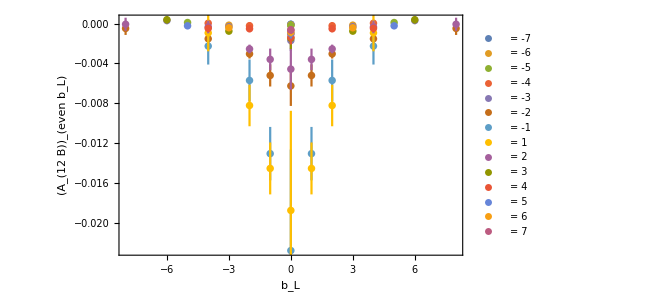

```mathematica
PlotA12B[8]
```

```mathematica
MemDBGet[platdb,MemDBSelect[platdb,{gammaValue->4,numberFilter->Im,linkPath->{2,2,2,2,2},sideLink->{1,1,1}}],data]
```

{⟨-0.0007 ± 0.002⟩_(RowBox[{)}

```mathematica
(*Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/eta_Pb_bsquare_A12B_err_AllMomentum.h5",Table["Pl-4/eta_"<>ToString[n]<>"_Pb_bsq_A12B_err"->PbbsqA12Bvalueserrbars[n],{n,1,10}],OverwriteTarget->"Append"]*)
```

```mathematica
(*datafor2dGaussianFitbLbTerrors={};
Do[
dataPointErr=MakeErrBars[PlotbLforDiffbTList[[TagbT]]];
Do[
AppendTo[datafor2dGaussianFitbLbTerrors,{{dataPointErr[[All,1]][[TagbL]][[1]],bTlist[[TagbT]],dataPointErr[[All,1]][[TagbL]][[2]]},dataPointErr[[All,2,1]][[TagbL]]}];
,{TagbL,Length[dataPointErr]}];
,{TagbT,Length[bTlist]}];
points=datafor2dGaussianFitbLbTerrors[[All,1]];
errors=datafor2dGaussianFitbLbTerrors[[All,2]];
Print[datafor2dGaussianFitbLbTerrors]

fitbLbLbT=NonlinearModelFit[points,A*Exp[-((alpha*()^2)+(beta*()^2))],{A,alpha, beta},{,},Weights->1/(errors[[All,2]]^2),Method->"LevenbergMarquardt",MaxIterations->10000];
Print["Fitting into   = ",Normal[fitbLbLbT]];
Print["\n             Fit dependence in  space"];
PlotfitbLbT=Show[PlotbL,Table[Plot[fitbLbLbT[x,bT],{x,Min[bLlist],Max[bLlist]},PlotStyle->ColorData[97,"ColorList"][[bT]]],{bT,1,Length[bTlist]}]];
Print[PlotfitbLbT];
Print["\n                 Cast in ,  space"];
FnbdotPbsqre[bp_,b2_]:=(A/.fitbLbLbT["BestFitParameters"])*Exp[-((bp^2)*(alpha/.fitbLbLbT["BestFitParameters"]))-(((b2) - (bp^2))*(beta/.fitbLbLbT["BestFitParameters"]))];
bsquarelist={1,4,9,16,25};
PlotbLdata= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Cast=Show[PlotbLdata,Table[Plot[FnbdotPbsqre[x,bsq],{x,Min[bLlist],Max[bLlist]}, Frame->True],{bsq,bsquarelist}]];
Print[Cast];
Print[" = ",bsquarelist]
Print["\n                 Fourier transform "];
xFourierTransf[x_, b2_]:= FourierTransform[(A/.fitbLbLbT["BestFitParameters"])*Exp[-((bp^2)*(alpha/.fitbLbLbT["BestFitParameters"]))-(((b2) - (bp^2))*(beta/.fitbLbLbT["BestFitParameters"]))],bp,x];
xFourier=Show[Table[Plot[xFourierTransf[x,bsq],{x,0,1}, AxesLabel->{x,None}],{bsq,bsquarelist}]];
Print[xFourier];
Print["\n    Normalize to -integrated Sivers shift, multiply by "];
xFourier=Show[Table[Plot[-x*xFourierTransf[x,bsq],{x,0,1}, AxesLabel->{x,None}],{bsq,bsquarelist}]];
Print[xFourier];*)
```